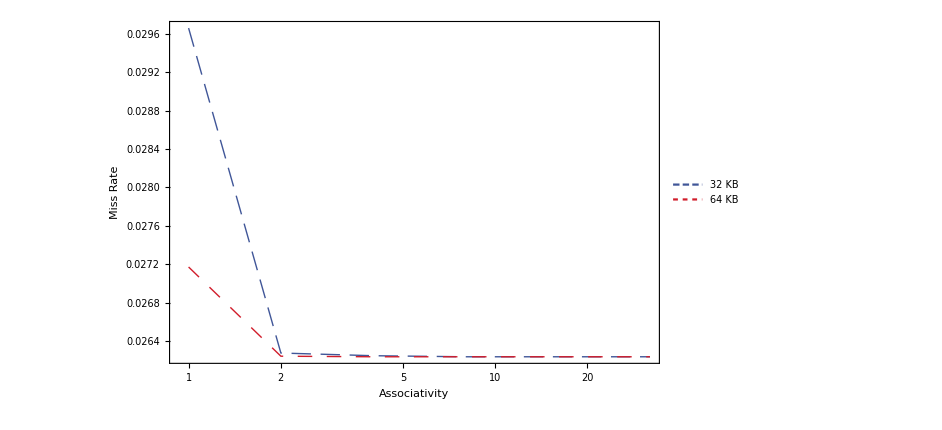

```mathematica
(*cache32klist={{1,0.014117},{2,0.012304},{4,0.012209},{8,0.012198},{16,0.012196},{32,0.012198}};
cache64klist={{1,0.012332},{2,0.012181},{4,0.012179},{8,0.012179},{16,0.012179},{32,0.012179}};*)

cache32klist={{1,0.029659},{2,0.026275},{4,0.026247},{8,0.026236},{16,0.026236},{32,0.026236}};
cache64klist={{1,0.027171},{2,0.026242},{4,0.026236},{8,0.026236},{16,0.026236},{32,0.026236}};

frame[legend_]:=Framed[legend,FrameStyle->{Black,Thin},RoundingRadius->5,Background->White];
ListLogLinearPlot[{cache32klist,cache64klist},PlotRange->{Full,Full},Joined->True,Frame->True,FrameTicks->{{All,None},{{1,2,4,8,16,32},None}},GridLines->{{1,2,4,8,16,32}, None},GridLinesStyle->{{LightGray,Thin},{LightGray,Thick}},
FrameStyle->Thickness[Medium],FrameTicksStyle->{{Directive[Black,FontFamily->"Helvetica",13],None},{Directive[Black,FontFamily->"Helvetica",13],None}},PlotStyle->{{RGBColor[64/255,86/255,152/255],Dashing[{0.02,0.01}],Thin},{RGBColor[209/255,29/255,43/255],Dashing[{0.015,0.015}],Thin},{RGBColor[0/255,156/255,4/255],Dashing[{0.01,0.007}],Thin},{RGBColor[227/255,131/255,0/255],Dashing[{0.013,0.01}],Thin},{RGBColor[121/255,17/255,152/255],Dashing[{0.01,0.01}],Thin}},PlotLegends->Placed[LineLegend[{"32 KB","64 KB","4 MB","32 MB"},LegendFunction->frame,LabelStyle->{13,FontFamily->"Helvetica"},LegendMarkerSize->{{50,4}}],{0.63,0.76}],
FrameLabel->{Style["Associativity",FontFamily->"Helvetica",Black,15],Style["Miss Rate",FontFamily->"Helvetica",Black,15]}]
```